# IPPT Model

## 3c. Multiple-Pulse Data Import

Description:
- This notebook will import the results from “3b. Multiple-Pulse Data Export” for any propellant choice.
- Results are imported from WDX format from desired file path on PC.

How to Run:
- First, evaluate notebooks 1 and 2b for propellant of choice. Export data using 3b to create a WDX or CSV file type.
- Pull the desired file to “Documents” folder on PC, or to whichever folder Mathematica is auto-tethered.
- Either click “Evaluate Notebook” in Menu Options or import file manually.

## Data Import

Notes:
- Adjust the date the file was produced and the shot number to reflect desired data source
- To print temporal data functions, toggle Timedata Boolean

```mathematica
Filedate = "2021-09-03";
Shotnum = "1"; 
Codeversion = "1.12";
Timedata = 0; (* Toggle for 1 -> single-pulse temporal data, 0 -> multi-pulse performance data *)

filename = StringJoin[Filedate,"_v",Codeversion,"_run_",Shotnum,".wdx"];
shotdata = Import[filename];
```

## Plot Styles

```mathematica
TimePlot[Fun_,Plotlabel_,Axislabel_,tmax_,scale_]:=Show[{Plot[Fun[t/10^6]scale,{t,0,10^6 tmax},PlotStyle->Black,PlotRange->All]},
Frame->True,
AspectRatio->1,
ImageSize->400,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"Time, t (μs)",Axislabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]
EffTimePlot[Fun_,Plotlabel_,Axislabel_,tmax_,scale_]:=Show[{Plot[Fun[t/10^6]scale,{t,0,10^6 tmax},PlotStyle->Black,PlotRange->{{0,10^6 tmax},{0,100}}]},
Frame->True,
AspectRatio->1,
ImageSize->400,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"Time, t (μs)",Axislabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]
PulsePlot[Table_,Plotlabel_,Axislabel_]:=
Show[{ListLinePlot[Table,PlotRange->All,Frame->True]},
ImageSize->400,
PlotLabel->StringJoin[Plotlabel," at Each Pulse"],
FrameLabel->{"Pulse",Axislabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle-> {FontFamily->"Times"}]
TimeCompPlot[Fun1_,Fun2_,Plotlabel_,Axislabel_,tmax_,scale_]:=Show[{Plot[{Fun1[t/10^6]scale,Fun2[t/10^6]scale},{t,0,10^6 tmax},PlotStyle->Black,PlotRange->All]},
Frame->True,
AspectRatio->1,
ImageSize->400,
PlotLabel-> StringJoin["Time-Evolutions of ",Plotlabel],
FrameLabel->{"Time, t (μs)",Axislabel},
PlotLegends-> {"Pulse 1","Steady state"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]
```

## Data Visualization

Axial boundary of simulation = 0.2 m

Number of axial gridpoints = 1000

Maximum time of simulation = 0.00002 s

Number of timesteps = 1000

Initial current sheet location = 0. m

Initial current sheet width = 0.002 m

Pre-ionization fraction = 1.

Pre-ionization length scale = 0.002 m

Characteristic ambient neutral density = 200000000000000000000 m^-3

Characteristic ambient neutral length scale = 0.02 m

Initial electron temperature = 20 eV

Initial ion temperature = 0.1 eV

Coil inductance = 1/500000 H

Stray inductance = 3/5000000 H

Coil resistance = 0.05 Ohms

Capacitance = 2 μF

Capacitor voltage = 5000 V

Coil mutual coupling distance = 0.04 m

Location of the coil with respect to the neutral gas injection plane = -0.002 m

Thruster outer radius = 0.1 m

Thruster inner radius = 0.03 m

Pulse repetition rate = 10 kHz

Number of pulses = 2

Isp (s) = {818.489,445.996}

Without energy recovery: ηT = {0.00979908,0.00500907}

With energy recovery: ηT = {0.0519815,0.0268768}

ηm = {0.604622,0.594897}

Πion (1) = {0.00133469,0.0000783161}

Πion (2) = {0.00020221,0.0000212389}

Πcex = {0.902615,0.935242}

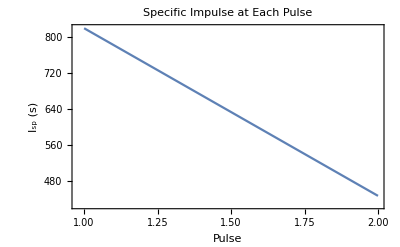

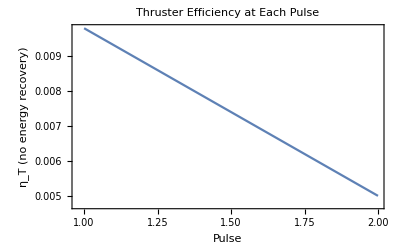

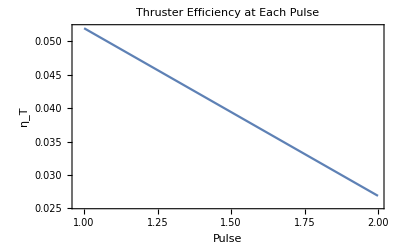

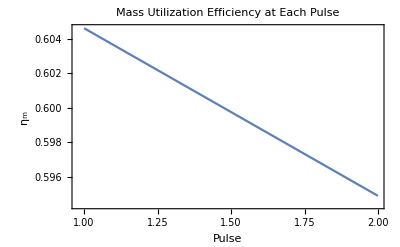

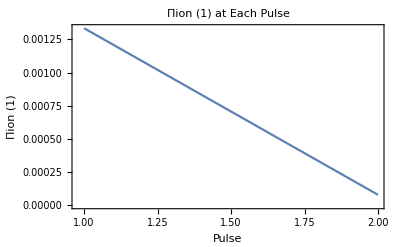

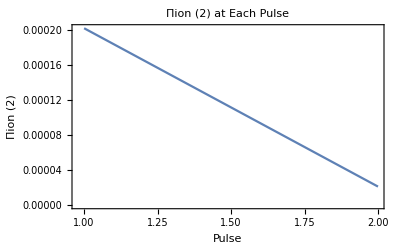

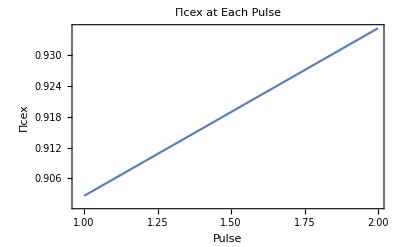

```mathematica
(* ICs *)
zmaxt=shotdata[[1]];
zstepst=shotdata[[2]];
tmaxt=shotdata[[3]];
tstepst=shotdata[[4]];
zs0t=shotdata[[5]];
ws0t=shotdata[[6]];
χi0t=shotdata[[7]];
zχit=shotdata[[8]];
nn0t=shotdata[[9]];
znt=shotdata[[10]];
Te0t=shotdata[[11]];
Ti0t=shotdata[[12]];
Lct=shotdata[[13]];
L0t=shotdata[[14]];
Rct=shotdata[[15]];
C0t=shotdata[[16]];
V0t=shotdata[[17]];
zct=shotdata[[18]];
zc0t=shotdata[[19]];
rtout=shotdata[[20]];
rtin=shotdata[[21]];
frept = shotdata[[22]];
Npt =shotdata[[23]]; 

If[Timedata==1,
(** Single-pulse data **)
(* State variables *)
nn=shotdata[[24]];
ws=shotdata[[25]];
zs=shotdata[[26]];
vs=shotdata[[27]];
vf=shotdata[[28]];
ns=shotdata[[29]];
nf=shotdata[[30]];
Ic=shotdata[[31]];
Ip=shotdata[[32]];
M=shotdata[[33]];
V=shotdata[[34]];
Te=shotdata[[35]];
Ti=shotdata[[36]];
ps=shotdata[[37]];
KEs=shotdata[[38]];
Ef=shotdata[[39]];
(* Performance metrics *)
mbit=shotdata[[40]];
ms[t_]=shotdata[[41]];
Epi=shotdata[[42]];
Eel=shotdata[[43]];
Eind[t_]=shotdata[[44]];
Ecap[t_]=shotdata[[45]];
Eke[t_]=shotdata[[46]];
EkePl[t_]=shotdata[[47]];
EkeEnt[t_]=shotdata[[48]];
Ete[t_]=shotdata[[49]];
Ibit[t_]=shotdata[[50]];
Isp[t_]=shotdata[[51]];
ηm[t_]=shotdata[[52]];
MassFrac[t_]=shotdata[[53]];
ηT[t_]=shotdata[[54]];
ηTrec[t_]=shotdata[[55]];
Πiont[t_]=shotdata[[56]];
Πiont2[t_]=shotdata[[57]];
Πcext2[t_]=shotdata[[58]];
,
(** Multi-pulse data **)
(* Point performance metrics *)
Isptable=shotdata[[24;;23+Npt]];
nttable=shotdata[[24+Npt;;23+2Npt]];
ntrectable=shotdata[[24+2Npt;;23+3Npt]];
nmtable=shotdata[[24+3Npt;;23+4Npt]];
piion1table=shotdata[[24+4Npt;;23+5Npt]];
piion2table=shotdata[[24+5Npt;;23+6Npt]];
picextable=shotdata[[24+6Npt;;23+7Npt]];
(* Initial state/performance *)
nni=shotdata[[24+7Npt]];
wsi=shotdata[[25+7Npt]];
zsi=shotdata[[26+7Npt]];
vsi=shotdata[[27+7Npt]];
vfi=shotdata[[28+7Npt]];
nsi=shotdata[[29+7Npt]];
nfi=shotdata[[30+7Npt]];
Ici=shotdata[[31+7Npt]];
Ipi=shotdata[[32+7Npt]];
Mi=shotdata[[33+7Npt]];
Vi=shotdata[[34+7Npt]];
Tei=shotdata[[35+7Npt]];
Tii=shotdata[[36+7Npt]];
psi=shotdata[[37+7Npt]];
KEsi=shotdata[[38+7Npt]];
Efi=shotdata[[39+7Npt]];
mbiti=shotdata[[40+7Npt]];
msi[t_]=shotdata[[41+7Npt]];
Epii=shotdata[[42+7Npt]];
Eeli=shotdata[[43+7Npt]];
Eindi[t_]=shotdata[[44+7Npt]];
Ecapi[t_]=shotdata[[45+7Npt]];
Ekei[t_]=shotdata[[46+7Npt]];
EkePli[t_]=shotdata[[47+7Npt]];
EkeEnti[t_]=shotdata[[48+7Npt]];
Etei[t_]=shotdata[[49+7Npt]];
Ibiti[t_]=shotdata[[50+7Npt]];
Ispi[t_]=shotdata[[51+7Npt]];
ηmi[t_]=shotdata[[52+7Npt]];
MassFraci[t_]=shotdata[[53+7Npt]];
ηTi[t_]=shotdata[[54+7Npt]];
ηTreci[t_]=shotdata[[55+7Npt]];
Πionti[t_]=shotdata[[56+7Npt]];
Πiont2i[t_]=shotdata[[57+7Npt]];
Πcext2i[t_]=shotdata[[58+7Npt]];
(* Final state/performance *)
nnf=shotdata[[59+7Npt]];
wsf=shotdata[[60+7Npt]];
zsf=shotdata[[61+7Npt]];
vsf=shotdata[[62+7Npt]];
vff=shotdata[[63+7Npt]];
nsf=shotdata[[64+7Npt]];
nff=shotdata[[65+7Npt]];
Icf=shotdata[[66+7Npt]];
Ipf=shotdata[[67+7Npt]];
Mf=shotdata[[68+7Npt]];
Vf=shotdata[[69+7Npt]];
Tef=shotdata[[70+7Npt]];
Tif=shotdata[[71+7Npt]];
psf=shotdata[[72+7Npt]];
KEsf=shotdata[[73+7Npt]];
Eff=shotdata[[74+7Npt]];
mbitf=shotdata[[75+7Npt]];
msf[t_]=shotdata[[76+7Npt]];
Epif=shotdata[[77+7Npt]];
Eelf=shotdata[[78+7Npt]];
Eindf[t_]=shotdata[[79+7Npt]];
Ecapf[t_]=shotdata[[80+7Npt]];
Ekef[t_]=shotdata[[81+7Npt]];
EkePlf[t_]=shotdata[[82+7Npt]];
EkeEntf[t_]=shotdata[[83+7Npt]];
Etef[t_]=shotdata[[84+7Npt]];
Ibitf[t_]=shotdata[[85+7Npt]];
Ispf[t_]=shotdata[[86+7Npt]];
ηmf[t_]=shotdata[[87+7Npt]];
MassFracf[t_]=shotdata[[88+7Npt]];
ηTf[t_]=shotdata[[89+7Npt]];
ηTrecf[t_]=shotdata[[90+7Npt]];
Πiontf[t_]=shotdata[[91+7Npt]];
Πiont2f[t_]=shotdata[[92+7Npt]];
Πcext2f[t_]=shotdata[[93+7Npt]];
];

(** Print ICs **)
Print["Axial boundary of simulation = ",zmaxt," m"];
Print["Number of axial gridpoints = ",zstepst];
Print["Maximum time of simulation = ",tmaxt," s"];
Print["Number of timesteps = ",tstepst];
Print["Initial current sheet location = ",zs0t," m"];
Print["Initial current sheet width = ",ws0t," m"];
Print["Pre-ionization fraction = ",χi0t];
Print["Pre-ionization length scale = ",zχit," m"];
Print["Characteristic ambient neutral density = ",nn0t," m^-3"];
Print["Characteristic ambient neutral length scale = ",znt," m"];
Print["Initial electron temperature = ",Te0t," eV"];
Print["Initial ion temperature = ",Ti0t," eV"];
Print["Coil inductance = ",Lct," H"];
Print["Stray inductance = ",L0t," H"];
Print["Coil resistance = ",Rct," Ohms"];
Print["Capacitance = ",C0t*10^6," μF"];
Print["Capacitor voltage = ",V0t," V"];
Print["Coil mutual coupling distance = ",zct," m"];
Print["Location of the coil with respect to the neutral gas injection plane = ",zc0t," m"];
Print["Thruster outer radius = ",rtout," m"];
Print["Thruster inner radius = ",rtin," m"];
Print["Pulse repetition rate = ",frept/10^3," kHz"];
Print["Number of pulses = ",Npt];

(** Plot Data **)
If[Timedata==1,
(** Time data **)
(* State variables *)
ec=1.60217662 10^-19; (* electron charge *)
Print[Plot3D[nn[z,t/10^6] 10^-20,{z,0,zmaxt},{t,0,tmaxt 10^6},
PlotRange->All,
ImageSize->400,
PlotLabel-> "Neutral Density Distribution",
AxesLabel->{"Position, z (m)","Time, t (μs)","n_n (×10^20 m^-3)"},
LabelStyle->{16,Black,FontFamily->"Times"},
ViewProjection->"Orthographic",
ViewPoint->{1,1,1}]];
Print[TimePlot[ws,"Sheet Width","w_s (m)",tmaxt,1]];
Print[TimePlot[zs,"Sheet Position","z_s (m)",tmaxt,1]];
Print[TimePlot[vs,"Sheet Velocity","v_s (km/s)",tmaxt,10^-3]];
Print[TimePlot[vf,"Entrained Neutral Velocity","v_f (km/s)",tmaxt,10^-3]];
Print[TimePlot[ns,"Sheet Density","n_s (m^-3)",tmaxt,1]];
Print[TimePlot[nf,"Entrained Neutral Density","n_f (m^-3)",tmaxt,1]];
Print[TimePlot[Ic,"Coil Current","I_c (kA)",tmaxt,10^-3]];
Print[TimePlot[Ip,"Plasma Current","I_p (kA)",tmaxt,10^-3]];
Print[TimePlot[M,"Mutual Inductance","M (nH)",tmaxt,10^9]];
Print[TimePlot[V,"Circuit Voltage","V_c (kV)",tmaxt,10^-3]];
Print[TimePlot[Te,"Electron Temperature","T_e (eV)",tmaxt,1]];
Print[TimePlot[Ti,"Ion Temperature","T_i (eV)",tmaxt,1]];
Print[TimePlot[ps,"Slipped Neutral Momentum","p_s (µN•s)",tmaxt,10^6]];
Print[TimePlot[KEs,"Kinetic Energy in Slipped Neutrals","KE_s (J)",tmaxt,1]];
Print[TimePlot[Ef,"Ionization Energy","E_f (J)",tmaxt,1]];
Print[Plot[ec 10^-3 ns[t/10^6]Te[t/10^6],{t,0,10^6 tmaxt},
PlotRange->All,
PlotStyle->Black,
Frame->True,
ImageSize->400,
PlotLabel-> "Time-Evolution of Sheet Pressure",
FrameLabel->{"Time, t (μs)","P_s (kPa)"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
Print[Plot[M[t/10^6]/Lct,{t,0,10^6 tmaxt},
PlotRange->{{0,10^6 tmaxt},{0,1}},
PlotStyle->Black,
Frame->True,
ImageSize->400,
PlotLabel-> "Time-Evolution of Coupling Coefficient",
FrameLabel->{"Time, t (μs)","k_0"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
(* Performance metrics *)
Print[TimePlot[ms,"Sheet Mass","m_s (kg)",tmaxt,1]];
Print[TimePlot[Eind,"Inductor Energy","E_ind (J)",tmaxt,1]];
Print[TimePlot[Ecap,"Capacitor Energy","E_cap (J)",tmaxt,1]];
Print[TimePlot[Eke,"Total Kinetic Energy","Energy (J)",tmaxt,1]];
Print[TimePlot[EkePl,"Kinetic Energy in Plasma","Energy (J)",tmaxt,1]];
Print[TimePlot[EkeEnt,"Kinetic Energy in Entrained Neutrals","Energy (J)",tmaxt,1]];
Print[TimePlot[Ete,"Thermal Energy","Energy (J)",tmaxt,1]];
Print[TimePlot[Ibit,"Impulse Bit","I_bit (N•s)",tmaxt,1]];
Print[TimePlot[Isp,"Specific Impulse","I_sp (s)",tmaxt,1]];
Print[EffTimePlot[ηm,"Mass Utilization Efficiency","η_m (%)",tmaxt,10^2]];

Print[EffTimePlot[ηT,"Thruster Efficiency","η_T no energy recovery (%)",tmaxt,10^2]];
Print[EffTimePlot[ηTrec,"Thruster Efficiency","η_T (%)",tmaxt,10^2]];
Print[TimePlot[Πiont,"Πion (1)","Πion (1)",tmaxt,1]];
Print[TimePlot[Πiont2,"Πion (2)","Πion (2)",tmaxt,1]];
Print[TimePlot[Πcext2,"Πcex","Πcex",tmaxt,1]];
Print[Plot[{Eke[t/10^6],EkePl[t/10^6],EkeEnt[t/10^6],Ete[t/10^6]},{t,0,10^6 tmaxt},
PlotRange->All,
Frame->True,
ImageSize->400,
PlotLabel-> "Energy Mode Comparison",
FrameLabel->{"Time, t (μs)","Energy (J)"},
PlotLegends->{"total kinetic energy","kinetic energy in plasma","kinetic energy in neutrals","total thermal energy"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
,
(** Multi-pulse data **)
Print["Isp (s) = ",Isptable];
Print["Without energy recovery: ηT = ",nttable];
Print["With energy recovery: ηT = ",ntrectable];
Print["ηm = ",nmtable];
Print["Πion (1) = ",piion1table];
Print["Πion (2) = ",piion2table];
Print["Πcex = ",picextable];
Print[PulsePlot[Isptable,"Specific Impulse","I_sp (s)"]];
Print[PulsePlot[nttable,"Thruster Efficiency","η_T (no energy recovery)"]];
Print[PulsePlot[ntrectable,"Thruster Efficiency","η_T"]];
Print[PulsePlot[nmtable,"Mass Utilization Efficiency","η_m"]];
Print[PulsePlot[piion1table,"Πion (1)","Πion (1)"]];
Print[PulsePlot[piion2table,"Πion (2)","Πion (2)"]];
Print[PulsePlot[picextable,"Πcex","Πcex"]];
];
```

## Neutral Density Evolution

Notes:
- Use slider bar to go forward or backward in time
- Shaded blue region shows current sheet location and width
- Solid black line shows ambient neutral density at a give timestep
- Dashed red line shows initial ambient neutral density

```mathematica
If[Timedata==1,
nsmax=Quiet[FindMaximum[ns[t],{t,tmaxt/10,0,tmaxt}]][[1]];
sliderplot=Manipulate[
Show[{
Plot[{nn[z,0],nn[z,t]},{z,0,0.2},PlotRange->{-0.1,1.05nn0t},PlotStyle->{{Dashed,Red},{Black}}],
ListPlot[{{zs[t],0},{zs[t],10 nn0t},{zs[t]+ws[t],0},{zs[t]+ws[t],10nn0t}},Joined->True,Filling->Axis,FillingStyle->{Blue,Opacity[0.4 ns[t]/nsmax]},PlotStyle->{Blue,Opacity[0.4 ns[t]/nsmax]}]
},
Frame->True,
AspectRatio->0.15,
ImageSize->900,
(* PlotLabel-> "Dynamic Time Plot of Neutral Entrainment", *)
FrameLabel->{"z (m)","n_n (m^-3)"},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.002],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}
]
,{t,0,tmaxt/2,tmaxt/250}]]
```

## Journal Paper Formatting

```mathematica
If[Timedata==1,
(** Energy Comparison **)
Eohmic=Interpolation[Table[{tt,NIntegrate[Rct Ic[dt]^2,{dt,0,tt}]},{tt,0,tmaxt,tmaxt/20}]];
Print[Plot[{Eke[t/10^6],EkePl[t/10^6],EkeEnt[t/10^6],KEs[t/10^6],Ete[t/10^6],Ef[t/10^6],Eohmic[t/10^6]},{t,0,10^6 tmaxt},
PlotRange->All,
Frame->True,
ImageSize->400,
PlotLabel-> "Energy Mode Comparison",
FrameLabel->{"Time, t (μs)","Energy (J)"},
PlotLegends->{"total kinetic energy","kinetic energy in plasma","kinetic energy in entrained neutrals","kinetic energy in slipped neutrals","thermal energy","ionization energy","ohmic energy"},
PlotStyle->{{Thick,Black},{Dashed,Red},Green,Orange,Purple,Blue,Cyan},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];

(** Adjust plot styles **)
TimePlot[Fun_,Axislabel_,tmax_,scale_]:=Show[{Plot[Fun[t/10^6]scale,{t,0,10^6 tmax},PlotStyle->Black,PlotRange->All]},
Frame->True,
AspectRatio->1,
FrameLabel->{"Time, t (μs)",Axislabel},
Axes->False,
LabelStyle->{12,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffTimePlot[Fun_,Axislabel_,tmax_,scale_]:=Show[{Plot[Fun[t/10^6]scale,{t,0,10^6 tmax},PlotStyle->Black,PlotRange->{{0,10^6 tmax},{0,100}}]},
Frame->True,
AspectRatio->1,
FrameLabel->{"Time, t (μs)",Axislabel},
Axes->False,
LabelStyle->{12,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** State variables **)
Print[GraphicsGrid[{
{TimePlot[vs,"Sheet Velocity, v_s (km/s)",tmaxt,10^-3],TimePlot[ws,"Sheet Width, w_s (m)",tmaxt,1],TimePlot[zs,"Sheet Position, z_s (m)",tmaxt,1]},
{TimePlot[ns,"Plasma Density, n_s (m^-3)",tmaxt,1],TimePlot[Te,"Electron Temp, T_e (eV)",tmaxt,1],TimePlot[Ti,"Ion Temp, T_i (eV)",tmaxt,1]},
{TimePlot[nf,"Ent. Neut. Dens. n_f (m^-3)",tmaxt,1],TimePlot[vf,"Ent. Neut. Vel. v_f (km/s)",tmaxt,10^-3],TimePlot[ps,"Neut. Slip Mom. p_s (μNs)",tmaxt,10^6]}}
,Spacings->{5,-5}, ImageSize-> 800]];

(** Performance metrics **)
EnergyFrac[t_]=(Eke[t]+KEs[t])/(Epi+Eel);

Print[GraphicsGrid[{
{TimePlot[Isp,"Specific Impulse, I_sp (s)",tmaxt,1],
TimePlot[Ibit,"Impulse Bit, I_bit (μNs)",tmaxt,10^6],EffTimePlot[ηTrec,"Thruster Efficiency, η_T (%)",tmaxt,10^2]},
{EffTimePlot[ηm,"Mass Utilization Efficiency, η_m (%)",tmaxt,10^2],
TimePlot[MassFrac,"Mass Fraction",tmaxt,1],
TimePlot[EnergyFrac,"Energy Fraction",tmaxt,1]}}
,Spacings->{5,5}, ImageSize-> 800]];

Print[GraphicsGrid[{
{TimePlot[Πiont,"Πion, LC time",tmaxt,1],
Plot[Πiont2[t/10^6],{t,0,10^6 tmaxt},PlotStyle->Black,PlotRange->{{0,10^6 tmaxt},{0,1}},
Frame->True,
AspectRatio->1,
FrameLabel->{"Time, t (μs)","Πion, Transit time"},
Axes->False,
LabelStyle->{12,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}],
TimePlot[Πcext2,"Πcex",tmaxt,1]}}
,Spacings->5, ImageSize-> 800]];

(** Plasma comparisons **)
ec=1.6 10^-19;    (* Electron Charge *)
me=9.11 10^-31;  (* Electron Mass *)

SlipLoss[t_]=nf[t](vs[t]-vf[t])UnitStep[(vs[t]-vf[t])];
(* Sion[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Argon *) *)
Sion[Te_]:= 10^-20 (-0.0001031 Te^2+6.386 Exp[-12.127/Te])(8ec Te/(π me))^(1/2); (* Xenon *)
IonGain[t_]=Sion[Te[t]] ns[t] nf[t] ws[t];

Print[Plot[{SlipLoss[t/10^6],IonGain[t/10^6]},{t,0,10^6 tmaxt},
PlotRange->All,
Frame->True,
ImageSize->400,
AspectRatio->1,
PlotLabel-> "Entrained Neutral Loss Rate Comparison",
FrameLabel->{"Time, t (μs)","Loss Rate (m^-2/s)"},
PlotLegends->{"Slip","Ionization"},
PlotStyle->{Thick,Dashed},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
Print[Plot[{ns[t/10^6] 10^-20,nf[t/10^6] 10^-20},{t,0,10^6 tmaxt},
PlotRange->All,
Frame->True,
ImageSize->400,
AspectRatio->1,
PlotLabel-> "Density Comparison",
FrameLabel->{"Time, t (μs)","Density (×10^20 m^-3)"},
PlotLegends->{"plasma sheet","entrained neutral"},
PlotStyle->{Thick,Dashed},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
Print[Plot[{vs[t/10^6] 10^-3,vf[t/10^6] 10^-3},{t,0,10^6 tmaxt},
PlotRange->All,
Frame->True,
ImageSize->400,
PlotLabel-> "Velocity Comparison",
FrameLabel->{"Time, t (μs)","Velocity (km/s)"},
PlotLegends->{"plasma sheet","entrained neutral"},
PlotStyle->{Thick,Dashed},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
Print[LogPlot[{Πiont[t/10^6],Πiont2[t/10^6],Πcext2[t/10^6]},{t,0,10^6 tmaxt},
PlotRange->All,
Frame->True,
ImageSize->400,
AspectRatio->1,
PlotLabel-> "Ionization Timescales",
FrameLabel->{"Time, t (μs)","Π_ionization"},
PlotLegends->{"LC time","Transit time","Charge exchange"},
PlotStyle->{Thick,Dashed},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
Print[LogPlot[{Πiont[t/10^6],Πiont2[t/10^6],Πcext2[t/10^6]},{t,0,10^6 tmaxt},
PlotRange->{{0,2.5},{10^-2,10^2}},
Frame->True,
ImageSize->400,
AspectRatio->1,
PlotLabel-> "Ionization Timescales",
FrameLabel->{"Time, t (μs)","Π_ionization"},
PlotLegends->{"LC time","Transit time","Charge exchange"},
PlotStyle->{Thick,Dashed},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]];
];
```